```mathematica
pic=ImageData[-Graphics-]⟦All,All,1⟧;
```

```mathematica
(*This loop searches for the first edge to work around*)For[x=2;s={};n=0,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,
xs=x;ys=y;x=480;y=640;s=Append[s,{xs,ys,pic⟦xs,ys⟧}]]]];
(*we consider 4 different directions, we always try to turn left if possible, think working through a maze with left hand on a wall*)dir={{0,1},{1,0},{0,-1},{-1,0}};
ds=1;
xc=33;yc=306;d=1;
While[xc≠ xs||yc≠ ys,n++;s=Append[s,{xc,yc ,pic⟦xc,yc⟧}];  If[pic⟦xc+dir⟦Mod[d-1,4,1],1⟧,yc+dir⟦Mod[d-1,4,1],2⟧⟧≠0,xc=xc+dir⟦Mod[d-1,4,1],1⟧;yc=yc+dir⟦Mod[d-1,4,1],2⟧;d=Mod[d-1,4,1],
If[pic⟦xc+dir⟦Mod[d,4,1],1⟧,yc+dir⟦Mod[d,4,1],2⟧⟧≠0,xc=xc+dir⟦Mod[d,4,1],1⟧;yc=yc+dir⟦Mod[d,4,1],2⟧;d=Mod[d,4,1],
If[pic⟦xc+dir⟦Mod[d+1,4,1],1⟧,yc+dir⟦Mod[d+1,4,1],2⟧⟧≠0,xc=xc+dir⟦Mod[d+1,4,1],1⟧;yc=yc+dir⟦Mod[d+1,4,1],2⟧;d=Mod[d+1,4,1],
If[pic⟦xc+dir⟦Mod[d+2,4,1],1⟧,yc+dir⟦Mod[d+2,4,1],2⟧⟧≠0,xc=xc+dir⟦Mod[d+2,4,1],1⟧;yc=yc+dir⟦Mod[d+2,4,1],2⟧;d=Mod[d+2,4,1]]]]]]
```

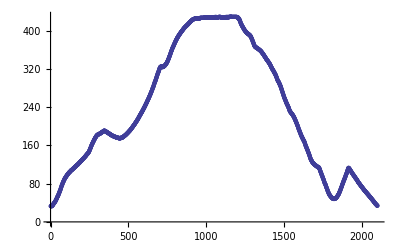

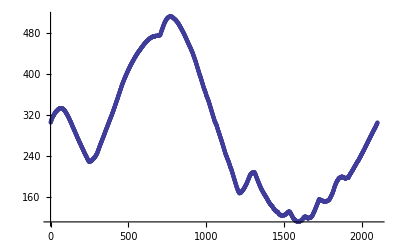

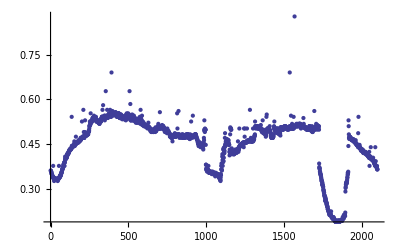

```mathematica
ListPlot[s⟦All,1⟧]
ListPlot[s⟦All,2⟧]
(*This is the depth information*)
ListPlot[s⟦All,3⟧]
```

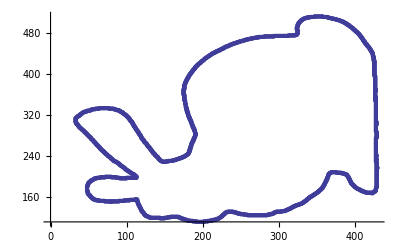

```mathematica
ListPlot[Table[{s⟦i,1⟧,s⟦i,2⟧},{i,1,Length[s]}]]
```

```mathematica
ListPointPlot3D[Table[{s⟦i,1⟧,s⟦i,2⟧,s⟦i,3⟧},{i,1,Length[s]}]]
```

-Graphics3D-

```mathematica
dir⟦Mod[3-1,4,1],1⟧
```

1

```mathematica
1
```

```mathematica
(* Directions, y+1,x+1,y-1,x-1
```

```mathematica
xs
```

3

```mathematica
For[x=2;s={},x<Dimensions[pic]⟦1⟧,x++,
For[y=2,y<Dimensions[pic]⟦2⟧,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,
xs=x;ys=y;x=Dimensions[pic]⟦1⟧;y=Dimensions[pic]⟦2⟧]]]
If[pic⟦xs,ys+1⟧≠0,xc=xs;yc=ys+1;d=1,If[pic⟦xs+1,ys⟧≠0,xc=xs+1;yc=ys;d=2,
If[pic⟦xs,ys-1⟧≠0,xc=xs;yc=ys-1;d=3,If[pic⟦xs-1,ys⟧≠0,xc=xs-1;yc=ys;d=4]]]];
n=1;
While[(xc≠xs||yc≠ys)&&n<2000,s=Append[s,{xc,yc ,pic⟦xc,yc⟧}];If[pic⟦xc,yc+1⟧≠0&&d≠3,yc++;d=1,If[pic⟦xc+1,yc⟧≠0&&d≠ 4,xc++;d=2,
If[pic⟦xc,yc-1⟧≠0&&d≠ 1,yc--;d=3,If[pic⟦xc-1,yc⟧≠0&&d≠2,xc--;d=4]]]];n++]
```

```mathematica
Length[s]
```

199

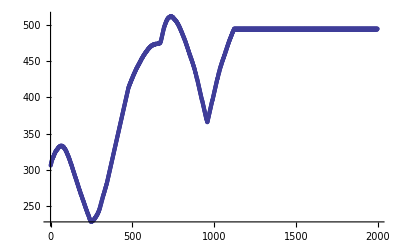

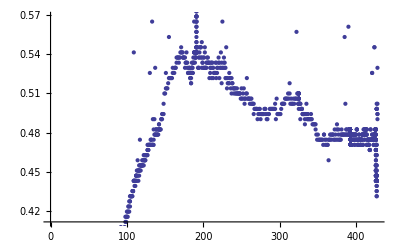

```mathematica
ListPlot[s⟦All,2⟧]
ListPlot[Table[{s⟦i,1⟧,s⟦i,3⟧},{i,1,Length[s]}]]
```

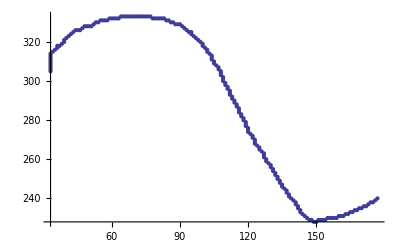

```mathematica
ListPlot[Table[{s⟦i,1⟧,s⟦i,2⟧},{i,1,Length[s]}]]
```

```mathematica
s
```

{{33,305,0.360784},{33,306,0.360784},{33,307,0.356863},{33,308,0.356863},«139054»,{36,318,0.376471},{37,318,0.337255},{38,318,0.337255},{38,319,0.333333}}

```mathematica
pic⟦xs,ys+1⟧
```

0.360784

```mathematica
While[
```

```mathematica
(*number of pixels on the edge of the image after removing isolated pixles*)
For[x=2;s={},x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0&&Min[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]==0,
s=Append[s,{x,y,255*pic⟦x,y⟧}]]]];
Length[s]
```

2130

```mathematica
s2=Table[s⟦i⟧,{i,2,Length[s]}];
t={s⟦1⟧};
For[j=1;k=1,j<Length[s],k=1;j++,
For[i=1,i<Length[s]+1-j,i++,
If[((t⟦j,1⟧-s2⟦i,1⟧)==0 &&(t⟦j,2⟧-s2⟦i,2⟧)^2 ==1)||((t⟦j,2⟧-s2⟦i,2⟧)==0 &&(t⟦j,1⟧-s2⟦i,1⟧)^2 ==1),k=i;i=Length[s]+1]];t=Append[t,s2⟦k⟧];s2=Delete[s2,{k}]]
```

```mathematica
t2=Table[t⟦i⟧,{i,2,Length[t]}];
u={t⟦1⟧};
For[j=1;k=1,j<Length[t],k=1;j++,
For[i=1,i<Length[t]+1-j,i++,
If[((u⟦j,1⟧-s2⟦i,1⟧)==0 &&(t⟦j,2⟧-s2⟦i,2⟧)^2 ==1)||((u⟦j,2⟧-s2⟦i,2⟧)==0 &&(t⟦j,1⟧-s2⟦i,1⟧)^2 ==1),k=i;i=Length[s]+1]];t=Append[t,s2⟦k⟧];s2=Delete[s2,{k}]]
```

```mathematica
Length[t]
```

2130

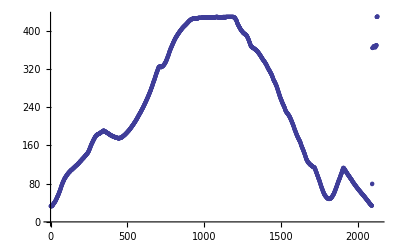

```mathematica
ListPlot[t⟦All,1⟧]
```

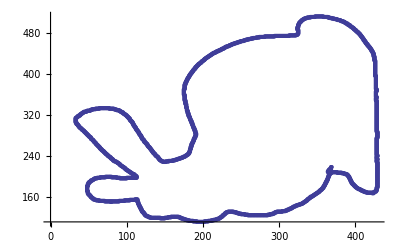

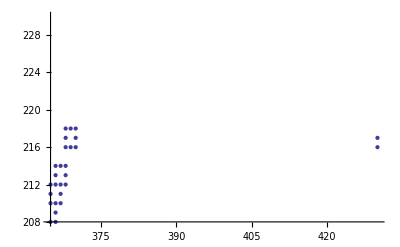

```mathematica
ListPlot[Table[{t⟦i,1⟧,t⟦i,2⟧},{i,1,2120}]]
ListPlot[Table[{t⟦i,1⟧,t⟦i,2⟧},{i,2100,2130}]]
```

```mathematica
(*number of peaks*)
For[x=2;n=0,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,If[pic⟦x,y⟧>Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧}]||pic⟦x,y⟧<Min[{If[pic⟦x+1,y+1⟧==0,1,pic⟦x+1,y+1⟧],If[pic⟦x+1,y⟧==0,1,pic⟦x+1,y⟧],If[pic⟦x+1,y-1⟧==0,1,pic⟦x+1,y-1⟧],If[pic⟦x,y+1⟧==0,1,pic⟦x,y+1⟧],If[pic⟦x-1,y+1⟧==0,1,pic⟦x-1,y+1⟧],If[pic⟦x-1,y⟧==0,1,pic⟦x-1,y⟧],If[pic⟦x-1,y-1⟧==0,1,pic⟦x-1,y-1⟧],If[pic⟦x,y-1⟧==0,1,pic⟦x,y-1⟧]}],n++]]]]
n
```

1582

```mathematica
(*number of peaks which are removed from the surface*)
For[x=2;n=0,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,If[pic⟦x,y⟧>Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]+2/255||pic⟦x,y⟧<Min[{If[pic⟦x+1,y+1⟧==0,1,pic⟦x+1,y+1⟧],If[pic⟦x+1,y⟧==0,1,pic⟦x+1,y⟧],If[pic⟦x+1,y-1⟧==0,1,pic⟦x+1,y-1⟧],If[pic⟦x,y+1⟧==0,1,pic⟦x,y+1⟧],If[pic⟦x-1,y+1⟧==0,1,pic⟦x-1,y+1⟧],If[pic⟦x-1,y⟧==0,1,pic⟦x-1,y⟧],If[pic⟦x-1,y-1⟧==0,1,pic⟦x-1,y-1⟧],If[pic⟦x,y-1⟧==0,1,pic⟦x,y-1⟧]}]-2/255,n++;s=Append[s,Abs[pic⟦x+1,y⟧+pic⟦x-1,y⟧+pic⟦x,y+1⟧+pic⟦x,y-1⟧-4pic⟦x,y⟧]]]]]]
```

```mathematica
(*number of points after wayward peaks are removed*)
For[x=2;n=0,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,If[pic⟦x,y⟧≤ Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]+2/255&&pic⟦x,y⟧≥ Min[{If[pic⟦x+1,y+1⟧==0,1,pic⟦x+1,y+1⟧],If[pic⟦x+1,y⟧==0,1,pic⟦x+1,y⟧],If[pic⟦x+1,y-1⟧==0,1,pic⟦x+1,y-1⟧],If[pic⟦x,y+1⟧==0,1,pic⟦x,y+1⟧],If[pic⟦x-1,y+1⟧==0,1,pic⟦x-1,y+1⟧],If[pic⟦x-1,y⟧==0,1,pic⟦x-1,y⟧],If[pic⟦x-1,y-1⟧==0,1,pic⟦x-1,y-1⟧],If[pic⟦x,y-1⟧==0,1,pic⟦x,y-1⟧]}]-2/255,n++]]]]
n
```

98148

```mathematica
(*number of points after wayward peaks are removed, which have any curvature*)
For[x=2;n=0,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,If[pic⟦x,y⟧≤ Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]+2/255&&pic⟦x,y⟧≥ Min[{If[pic⟦x+1,y+1⟧==0,1,pic⟦x+1,y+1⟧],If[pic⟦x+1,y⟧==0,1,pic⟦x+1,y⟧],If[pic⟦x+1,y-1⟧==0,1,pic⟦x+1,y-1⟧],If[pic⟦x,y+1⟧==0,1,pic⟦x,y+1⟧],If[pic⟦x-1,y+1⟧==0,1,pic⟦x-1,y+1⟧],If[pic⟦x-1,y⟧==0,1,pic⟦x-1,y⟧],If[pic⟦x-1,y-1⟧==0,1,pic⟦x-1,y-1⟧],If[pic⟦x,y-1⟧==0,1,pic⟦x,y-1⟧]}]-2/255,If[Abs[pic⟦x+1,y⟧+pic⟦x-1,y⟧+pic⟦x,y+1⟧+pic⟦x,y-1⟧-4pic⟦x,y⟧]>0,n++]]]]]
n
```

78037

```mathematica
(*number of points after wayward peaks are removed, which have any gradient*)
For[x=2;n=0,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,If[pic⟦x,y⟧≤ Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]+2/255&&pic⟦x,y⟧≥ Min[{If[pic⟦x+1,y+1⟧==0,1,pic⟦x+1,y+1⟧],If[pic⟦x+1,y⟧==0,1,pic⟦x+1,y⟧],If[pic⟦x+1,y-1⟧==0,1,pic⟦x+1,y-1⟧],If[pic⟦x,y+1⟧==0,1,pic⟦x,y+1⟧],If[pic⟦x-1,y+1⟧==0,1,pic⟦x-1,y+1⟧],If[pic⟦x-1,y⟧==0,1,pic⟦x-1,y⟧],If[pic⟦x-1,y-1⟧==0,1,pic⟦x-1,y-1⟧],If[pic⟦x,y-1⟧==0,1,pic⟦x,y-1⟧]}]-2/255,If[(Abs[pic⟦x+1,y⟧-pic⟦x-1,y⟧]>0||Abs[pic⟦x,y+1⟧-pic⟦x,y-1⟧]>0),n++]]]]]
n
```

78626

```mathematica
(*number of points after wayward peaks are removed, which have curvature and gradient*)
For[x=2;n=0,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,If[pic⟦x,y⟧≤ Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]+2/255&&pic⟦x,y⟧≥ Min[{If[pic⟦x+1,y+1⟧==0,1,pic⟦x+1,y+1⟧],If[pic⟦x+1,y⟧==0,1,pic⟦x+1,y⟧],If[pic⟦x+1,y-1⟧==0,1,pic⟦x+1,y-1⟧],If[pic⟦x,y+1⟧==0,1,pic⟦x,y+1⟧],If[pic⟦x-1,y+1⟧==0,1,pic⟦x-1,y+1⟧],If[pic⟦x-1,y⟧==0,1,pic⟦x-1,y⟧],If[pic⟦x-1,y-1⟧==0,1,pic⟦x-1,y-1⟧],If[pic⟦x,y-1⟧==0,1,pic⟦x,y-1⟧]}]-2/255,If[(Abs[pic⟦x+1,y⟧-pic⟦x-1,y⟧]>0||Abs[pic⟦x,y+1⟧-pic⟦x,y-1⟧]>0)&&(Abs[pic⟦x+1,y⟧+pic⟦x-1,y⟧+pic⟦x,y+1⟧+pic⟦x,y-1⟧-4pic⟦x,y⟧]>0),n++]]]]]
n
```

72218

```mathematica
(*number of points as a function of curvature*)
For[x=2;n={},x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,If[pic⟦x,y⟧≤ Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]+2/255&&pic⟦x,y⟧≥ Min[{If[pic⟦x+1,y+1⟧==0,1,pic⟦x+1,y+1⟧],If[pic⟦x+1,y⟧==0,1,pic⟦x+1,y⟧],If[pic⟦x+1,y-1⟧==0,1,pic⟦x+1,y-1⟧],If[pic⟦x,y+1⟧==0,1,pic⟦x,y+1⟧],If[pic⟦x-1,y+1⟧==0,1,pic⟦x-1,y+1⟧],If[pic⟦x-1,y⟧==0,1,pic⟦x-1,y⟧],If[pic⟦x-1,y-1⟧==0,1,pic⟦x-1,y-1⟧],If[pic⟦x,y-1⟧==0,1,pic⟦x,y-1⟧]}]-2/255,s=Append[s,Abs[pic⟦x+1,y⟧+pic⟦x-1,y⟧+pic⟦x,y+1⟧+pic⟦x,y-1⟧-4pic⟦x,y⟧]]]]]]
```

{}

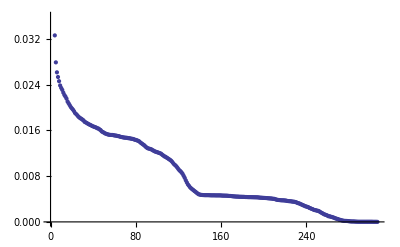

```mathematica
Delete[BinCounts[255*s],{1}];
Table[{j-1,(98148-Sum[%⟦i⟧,{i,1,j}])/98148},{j,1,Length[%]}]//N;
ListPlot[%]
```

```mathematica
Length[s]
255*Max[s]
```

581

7.

```mathematica
RankedMax[{1,2,3,4,1,5,5},3]
```

4

```mathematica
Length[s]
Sort[255*s,#1>#2&]
```

1001

{94.,46.,35.,25.,25.,23.,22.,21.,21.,17.,16.,15.,15.,14.,14.,13.,12.,12.,12.,11.,11.,11.,10.,10.,10.,10.,10.,10.,9.,9.,9.,8.,7.,7.,7.,7.,6.,5.,5.,5.,5.,5.,5.,4.,4.,4.,4.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
For[x=2;n=0,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,If[(pic⟦x+1,y⟧-pic⟦x,y⟧)*(pic⟦x,y⟧-pic⟦x-1,y⟧)>0||(pic⟦x,y⟧-pic⟦x,y+1⟧)*(pic⟦x,y⟧-pic⟦x,y-1⟧)>0
,,n++]]]];
n
```

76043

```mathematica
For[x=2;n=0,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,If[(pic⟦x+1,y⟧-pic⟦x,y⟧)*(pic⟦x,y⟧-pic⟦x-1,y⟧)≥0||(pic⟦x,y⟧-pic⟦x,y+1⟧)*(pic⟦x,y⟧-pic⟦x,y-1⟧)≥0
,,n++]]]];
n
```

625

```mathematica
ListPointPlot3D[s1]
```

-Graphics3D-

```mathematica
Interpolation[Table[{{s1⟦i,1⟧,s1⟦i,2⟧},s1⟦i,3⟧/255},{i,1,Length[s1]}]]
pic1=Table[Ceiling[pic⟦X,Y⟧]*%[X,Y],{X,1,480},{Y,1,640}];
{Image[pic],Image[pic1]}
```

InterpolatingFunction[{{33.,430.},{111.,512.}},<>]

{-Graphics-,-Graphics-}

```mathematica
Image[10*Abs[pic1-pic]]
```

-Graphics-

```mathematica
s2=Table[s1⟦i⟧,{i,2,Length[s1]}];
t={s1⟦1⟧};
For[j=1;k=1,j<Length[s1],k=1;j++,
For[i=1,i<Length[s1]+1-j,i++,
If[((t⟦j,1⟧-s2⟦k,1⟧)^2+(t⟦j,2⟧-s2⟦k,2⟧)^2+(t⟦j,3⟧-s2⟦k,3⟧)^2)>((t⟦j,1⟧-s2⟦i,1⟧)^2+(t⟦j,2⟧-s2⟦i,2⟧)^2+(t⟦j,3⟧-s2⟦i,3⟧)^2),k=i]];t=Append[t,s2⟦k⟧];s2=Delete[s2,{k}]]
```

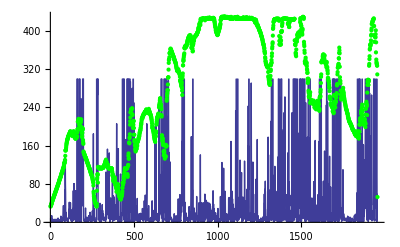

```mathematica
ListLinePlot[Table[(t⟦i+1,1⟧-t⟦i,1⟧)^2+(t⟦i+1,2⟧-t⟦i,2⟧)^2+(t⟦i+1,3⟧-t⟦i,3⟧)^2,{i,1,Length[t]-1}],PlotRange->{0,300}];
ListPlot[t⟦All,1⟧,PlotStyle->Green];
Show[{%%,%},PlotRange->All]
```

```mathematica
{Interpolation[t⟦All,1⟧,InterpolationOrder->2],Interpolation[t⟦All,2⟧,InterpolationOrder->2],Interpolation[t⟦All,3⟧,InterpolationOrder->2]};
ParametricPlot3D[{%⟦1⟧[X],%⟦2⟧[X],%⟦3⟧[X]},{X,1,Length[t]}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[t]
```

```mathematica
MovingAverage[tt⟦All,1⟧,2]//N;
Interpolation[%]
Sum[{(%[(Length[%%] X)/Length[tt]]-tt⟦X,1⟧)^2/Length[%%]-(%[(Length[%%] X)/Length[tt]]-tt⟦X,1⟧)^2/Length[tt]},{X,1,Length[tt]}]
MovingAverage[tt⟦All,1⟧,5]//N;
Interpolation[%]
Sum[{(%[(Length[%%] X)/Length[tt]]-tt⟦X,1⟧)^2/Length[%%]-(%[(Length[%%] X)/Length[tt]]-tt⟦X,1⟧)^2/Length[tt]},{X,1,Length[tt]}]
MovingAverage[tt⟦All,1⟧,10]//N;
Interpolation[%]
Sum[{(%[(Length[%%] X)/Length[tt]]-tt⟦X,1⟧)^2/Length[%%]-(%[(Length[%%] X)/Length[tt]]-tt⟦X,1⟧)^2/Length[tt]},{X,1,Length[tt]}]
MovingAverage[tt⟦All,1⟧,15]//N;
Interpolation[%]
Sum[{(%[(Length[%%] X)/Length[tt]]-tt⟦X,1⟧)^2/Length[%%]-(%[(Length[%%] X)/Length[tt]]-tt⟦X,1⟧)^2/Length[tt]},{X,1,Length[tt]}]
MovingAverage[tt⟦All,1⟧,20]//N;
Interpolation[%]
Sum[{(%[(Length[%%] X)/Length[tt]]-tt⟦X,1⟧)^2/Length[%%]-(%[(Length[%%] X)/Length[tt]]-tt⟦X,1⟧)^2/Length[tt]},{X,1,Length[tt]}]
```

InterpolatingFunction[{{1.,499.}},<>]

{0.000190664}

InterpolatingFunction[{{1.,496.}},<>]

{0.00873276}

InterpolatingFunction[{{1.,491.}},<>]

{0.0949888}

InterpolatingFunction[{{1.,486.}},<>]

{0.35846}

InterpolatingFunction[{{1.,481.}},<>]

{0.905128}

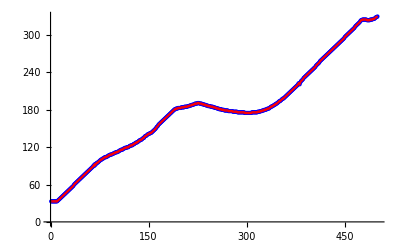

-Graphics-

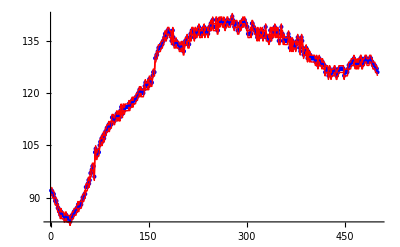

```mathematica
Show[ListPlot[tt⟦All,3⟧,PlotStyle->Blue],ListLinePlot[{tt⟦All,3⟧+0.86,tt⟦All,3⟧-1.076},PlotStyle->Red]]
```

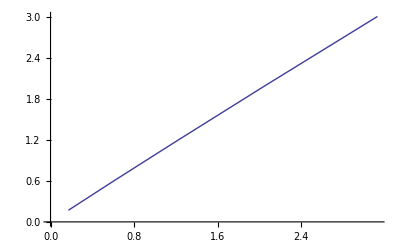

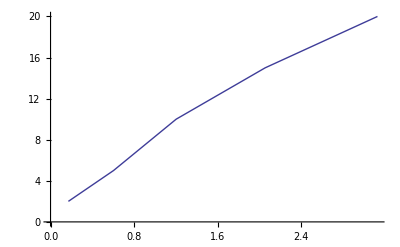

InterpolatingFunction[{{1.,496.}},<>]

InterpolatingFunction[{{1.,491.}},<>]

InterpolatingFunction[{{1.,486.}},<>]

{2.05629,1.99871}

InterpolatingFunction[{{1.,481.}},<>]

```mathematica
ListLinePlot[{{0.1709986079239173,0.17065661070806948},{0.6035111447224433,0.5986830555646637},{1.2036155837540332,1.1819505032464608},{2.0562911395180348,1.9987149876115295},{3.1319800107715263,3.0129647703622084}}]
ListLinePlot[{{0.1709986079239173,2},{0.6035111447224433,5},{1.2036155837540332,10},{2.0562911395180348,15},{3.1319800107715263,20}}]
```

```mathematica
points=44;
1/(points-2)Sum[{(tt⟦i+1,1⟧+tt⟦i-1,1⟧-2tt⟦i,1⟧)^2,(tt⟦i+1,2⟧+tt⟦i-1,2⟧-2tt⟦i,2⟧)^2,(tt⟦i+1,3⟧+tt⟦i-1,3⟧-2tt⟦i,3⟧)^2},{i,2,points-1}]//N
1/(points-1)Sum[{(tt⟦i+1,1⟧-tt⟦i,1⟧)^2,(tt⟦i+1,2⟧-tt⟦i,2⟧)^2,(tt⟦i+1,3⟧-tt⟦i,3⟧)^2},{i,1,points-1}]//N
```

{0.0714286,0.309524,1.07143}

{0.860465,0.697674,0.465116}

116

0.982275

119

0.983584

122

0.978108

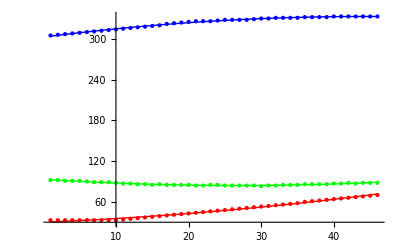

-Graphics3D-

```mathematica
points=44;
col={Red,Green,Blue};
order=5;
q1={Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,1⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,2⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,3⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X]};
Table[{(tt⟦X,1⟧-q⟦1⟧)^2,(tt⟦X,2⟧-q⟦2⟧)^2,(tt⟦X,3⟧-q⟦3⟧)^2},{X,1,points}];
{Max[%⟦All,1⟧],Max[%⟦All,2⟧],Max[%⟦All,3⟧]};
Sum[(499(tt⟦X,1⟧-q⟦1⟧)^2)/381+(499(tt⟦X,2⟧-q⟦2⟧)^2)/496+(499(tt⟦X,3⟧-q⟦3⟧)^2)/548,{X,1,points}];
df=3*points-3*order-1
Gamma[df/2,(%%)/2]/Gamma[df/2]
points=45;
col={Red,Green,Blue};
order=5;
q1={Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,1⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,2⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,3⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X]};
Table[{(tt⟦X,1⟧-q⟦1⟧)^2,(tt⟦X,2⟧-q⟦2⟧)^2,(tt⟦X,3⟧-q⟦3⟧)^2},{X,1,points}];
{Max[%⟦All,1⟧],Max[%⟦All,2⟧],Max[%⟦All,3⟧]};
Sum[(499(tt⟦X,1⟧-q⟦1⟧)^2)/381+(499(tt⟦X,2⟧-q⟦2⟧)^2)/496+(499(tt⟦X,3⟧-q⟦3⟧)^2)/548,{X,1,points}];
df=3*points-3*order-1
Gamma[df/2,(%%)/2]/Gamma[df/2]
points=46;
col={Red,Green,Blue};
order=5;
q1={Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,1⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,2⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,3⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X]};
Table[{(tt⟦X,1⟧-q⟦1⟧)^2,(tt⟦X,2⟧-q⟦2⟧)^2,(tt⟦X,3⟧-q⟦3⟧)^2},{X,1,points}];
{Max[%⟦All,1⟧],Max[%⟦All,2⟧],Max[%⟦All,3⟧]};
Sum[(499(tt⟦X,1⟧-q⟦1⟧)^2)/381+(499(tt⟦X,2⟧-q⟦2⟧)^2)/496+(499(tt⟦X,3⟧-q⟦3⟧)^2)/548,{X,1,points}];
df=3*points-3*order-1
Gamma[df/2,(%%)/2]/Gamma[df/2]
Show[{Plot[q⟦1⟧,{X,1,points},PlotStyle->Red],ListPlot[Table[tt⟦X,1⟧,{X,1,points}],PlotStyle->Red],Plot[q⟦2⟧,{X,1,points},PlotStyle->Blue],ListPlot[Table[tt⟦X,2⟧,{X,1,points}],PlotStyle->Blue],Plot[q⟦3⟧,{X,1,points},PlotStyle->Green],ListPlot[Table[tt⟦X,3⟧,{X,1,points}],PlotStyle->Green]},PlotRange->All]
Show[ListPointPlot3D[Table[tt⟦X⟧,{X,1,points}]],ParametricPlot3D[{q⟦1⟧,q⟦2⟧,q⟦3⟧},{X,1,points}]]
```

```mathematica
points=44;
col={Red,Green,Blue};
order=4;
q1={Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,1⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,2⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,3⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X]};
Table[{(tt⟦X,1⟧-q⟦1⟧)^2,(tt⟦X,2⟧-q⟦2⟧)^2,(tt⟦X,3⟧-q⟦3⟧)^2},{X,1,points}];
{Max[%⟦All,1⟧],Max[%⟦All,2⟧],Max[%⟦All,3⟧]};
Sum[(499(tt⟦X,1⟧-q⟦1⟧)^2)/381+(499(tt⟦X,2⟧-q⟦2⟧)^2)/496+(499(tt⟦X,3⟧-q⟦3⟧)^2)/548,{X,1,points}];
df=3*points-3*order-1
Gamma[df/2,(%%)/2]/Gamma[df/2]
points=45;
col={Red,Green,Blue};
order=4;
q1={Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,1⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,2⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,3⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X]};
Table[{(tt⟦X,1⟧-q⟦1⟧)^2,(tt⟦X,2⟧-q⟦2⟧)^2,(tt⟦X,3⟧-q⟦3⟧)^2},{X,1,points}];
{Max[%⟦All,1⟧],Max[%⟦All,2⟧],Max[%⟦All,3⟧]};
Sum[(499(tt⟦X,1⟧-q⟦1⟧)^2)/381+(499(tt⟦X,2⟧-q⟦2⟧)^2)/496+(499(tt⟦X,3⟧-q⟦3⟧)^2)/548,{X,1,points}];
df=3*points-3*order-1
Gamma[df/2,(%%)/2]/Gamma[df/2]
points=46;
col={Red,Green,Blue};
order=4;
q1={Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,1⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,2⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,3⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X]};
Table[{(tt⟦X,1⟧-q⟦1⟧)^2,(tt⟦X,2⟧-q⟦2⟧)^2,(tt⟦X,3⟧-q⟦3⟧)^2},{X,1,points}];
{Max[%⟦All,1⟧],Max[%⟦All,2⟧],Max[%⟦All,3⟧]};
Sum[(499(tt⟦X,1⟧-q⟦1⟧)^2)/381+(499(tt⟦X,2⟧-q⟦2⟧)^2)/496+(499(tt⟦X,3⟧-q⟦3⟧)^2)/548,{X,1,points}];
df=3*points-3*order-1
Gamma[df/2,(%%)/2]/Gamma[df/2]
Show[{Plot[q⟦1⟧,{X,1,points},PlotStyle->Red],ListPlot[Table[tt⟦X,1⟧,{X,1,points}],PlotStyle->Red],Plot[q⟦2⟧,{X,1,points},PlotStyle->Blue],ListPlot[Table[tt⟦X,2⟧,{X,1,points}],PlotStyle->Blue],Plot[q⟦3⟧,{X,1,points},PlotStyle->Green],ListPlot[Table[tt⟦X,3⟧,{X,1,points}],PlotStyle->Green]},PlotRange->All]
Show[ListPointPlot3D[Table[tt⟦X⟧,{X,1,points}]],ParametricPlot3D[{q⟦1⟧,q⟦2⟧,q⟦3⟧},{X,1,points}]]
```

119

0.989541

122

0.990301

125

0.986677

-Graphics-

-Graphics3D-

```mathematica
points=44;
col={Red,Green,Blue};
order=3;
q1={Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,1⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,2⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,3⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X]};
Table[{(tt⟦X,1⟧-q⟦1⟧)^2,(tt⟦X,2⟧-q⟦2⟧)^2,(tt⟦X,3⟧-q⟦3⟧)^2},{X,1,points}];
{Max[%⟦All,1⟧],Max[%⟦All,2⟧],Max[%⟦All,3⟧]};
Sum[(499(tt⟦X,1⟧-q⟦1⟧)^2)/381+(499(tt⟦X,2⟧-q⟦2⟧)^2)/496+(499(tt⟦X,3⟧-q⟦3⟧)^2)/548,{X,1,points}];
df=3*points-3*order-1
Gamma[df/2,(%%)/2]/Gamma[df/2]
points=45;
col={Red,Green,Blue};
order=3;
q1={Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,1⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,2⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,3⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X]};
Table[{(tt⟦X,1⟧-q⟦1⟧)^2,(tt⟦X,2⟧-q⟦2⟧)^2,(tt⟦X,3⟧-q⟦3⟧)^2},{X,1,points}];
{Max[%⟦All,1⟧],Max[%⟦All,2⟧],Max[%⟦All,3⟧]};
Sum[(499(tt⟦X,1⟧-q⟦1⟧)^2)/381+(499(tt⟦X,2⟧-q⟦2⟧)^2)/496+(499(tt⟦X,3⟧-q⟦3⟧)^2)/548,{X,1,points}];
df=3*points-3*order-1
Gamma[df/2,(%%)/2]/Gamma[df/2]
points=46;
col={Red,Green,Blue};
order=3;
q1={Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,1⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,2⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,3⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X]};
Table[{(tt⟦X,1⟧-q⟦1⟧)^2,(tt⟦X,2⟧-q⟦2⟧)^2,(tt⟦X,3⟧-q⟦3⟧)^2},{X,1,points}];
{Max[%⟦All,1⟧],Max[%⟦All,2⟧],Max[%⟦All,3⟧]};
Sum[(499(tt⟦X,1⟧-q⟦1⟧)^2)/381+(499(tt⟦X,2⟧-q⟦2⟧)^2)/496+(499(tt⟦X,3⟧-q⟦3⟧)^2)/548,{X,1,points}];
df=3*points-3*order-1
Gamma[df/2,(%%)/2]/Gamma[df/2]
Show[{Plot[q⟦1⟧,{X,1,points},PlotStyle->Red],ListPlot[Table[tt⟦X,1⟧,{X,1,points}],PlotStyle->Red],Plot[q⟦2⟧,{X,1,points},PlotStyle->Blue],ListPlot[Table[tt⟦X,2⟧,{X,1,points}],PlotStyle->Blue],Plot[q⟦3⟧,{X,1,points},PlotStyle->Green],ListPlot[Table[tt⟦X,3⟧,{X,1,points}],PlotStyle->Green]},PlotRange->All]
Show[ListPointPlot3D[Table[tt⟦X⟧,{X,1,points}]],ParametricPlot3D[{q⟦1⟧,q⟦2⟧,q⟦3⟧},{X,1,points}]]
```

122

0.99403

125

0.994453

128

0.992143

-Graphics-

-Graphics3D-

```mathematica
points=44;
col={Red,Green,Blue};
order=2;
q1={Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,1⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,2⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,3⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X]};
Table[{(tt⟦X,1⟧-q⟦1⟧)^2,(tt⟦X,2⟧-q⟦2⟧)^2,(tt⟦X,3⟧-q⟦3⟧)^2},{X,1,points}];
{Max[%⟦All,1⟧],Max[%⟦All,2⟧],Max[%⟦All,3⟧]};
Sum[(499(tt⟦X,1⟧-q⟦1⟧)^2)/381+(499(tt⟦X,2⟧-q⟦2⟧)^2)/496+(499(tt⟦X,3⟧-q⟦3⟧)^2)/548,{X,1,points}];
df=3*points-3*order-1
Gamma[df/2,(%%)/2]/Gamma[df/2]
points=45;
col={Red,Green,Blue};
order=2;
q1={Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,1⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,2⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,3⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X]};
Table[{(tt⟦X,1⟧-q⟦1⟧)^2,(tt⟦X,2⟧-q⟦2⟧)^2,(tt⟦X,3⟧-q⟦3⟧)^2},{X,1,points}];
{Max[%⟦All,1⟧],Max[%⟦All,2⟧],Max[%⟦All,3⟧]};
Sum[(499(tt⟦X,1⟧-q⟦1⟧)^2)/381+(499(tt⟦X,2⟧-q⟦2⟧)^2)/496+(499(tt⟦X,3⟧-q⟦3⟧)^2)/548,{X,1,points}];
df=3*points-3*order-1
Gamma[df/2,(%%)/2]/Gamma[df/2]
points=46;
col={Red,Green,Blue};
order=2;
q1={Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,1⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,2⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,3⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X]};
Table[{(tt⟦X,1⟧-q⟦1⟧)^2,(tt⟦X,2⟧-q⟦2⟧)^2,(tt⟦X,3⟧-q⟦3⟧)^2},{X,1,points}];
{Max[%⟦All,1⟧],Max[%⟦All,2⟧],Max[%⟦All,3⟧]};
Sum[(499(tt⟦X,1⟧-q⟦1⟧)^2)/381+(499(tt⟦X,2⟧-q⟦2⟧)^2)/496+(499(tt⟦X,3⟧-q⟦3⟧)^2)/548,{X,1,points}];
df=3*points-3*order-1
Gamma[df/2,(%%)/2]/Gamma[df/2]
Show[{Plot[q⟦1⟧,{X,1,points},PlotStyle->Red],ListPlot[Table[tt⟦X,1⟧,{X,1,points}],PlotStyle->Red],Plot[q⟦2⟧,{X,1,points},PlotStyle->Blue],ListPlot[Table[tt⟦X,2⟧,{X,1,points}],PlotStyle->Blue],Plot[q⟦3⟧,{X,1,points},PlotStyle->Green],ListPlot[Table[tt⟦X,3⟧,{X,1,points}],PlotStyle->Green]},PlotRange->All]
Show[ListPointPlot3D[Table[tt⟦X⟧,{X,1,points}]],ParametricPlot3D[{q⟦1⟧,q⟦2⟧,q⟦3⟧},{X,1,points}]]
```

125

0.996703

128

0.996928

131

0.995509

-Graphics-

-Graphics3D-

```mathematica
points=44;
col={Red,Green,Blue};
order=1;
q1={Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,1⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,2⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,3⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X]};
Table[{(tt⟦X,1⟧-q⟦1⟧)^2,(tt⟦X,2⟧-q⟦2⟧)^2,(tt⟦X,3⟧-q⟦3⟧)^2},{X,1,points}];
{Max[%⟦All,1⟧],Max[%⟦All,2⟧],Max[%⟦All,3⟧]};
Sum[(499(tt⟦X,1⟧-q⟦1⟧)^2)/381+(499(tt⟦X,2⟧-q⟦2⟧)^2)/496+(499(tt⟦X,3⟧-q⟦3⟧)^2)/548,{X,1,points}];
df=3*points-3*order-1
Gamma[df/2,(%%)/2]/Gamma[df/2]
points=45;
col={Red,Green,Blue};
order=1;
q1={Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,1⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,2⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,3⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X]};
Table[{(tt⟦X,1⟧-q⟦1⟧)^2,(tt⟦X,2⟧-q⟦2⟧)^2,(tt⟦X,3⟧-q⟦3⟧)^2},{X,1,points}];
{Max[%⟦All,1⟧],Max[%⟦All,2⟧],Max[%⟦All,3⟧]};
Sum[(499(tt⟦X,1⟧-q⟦1⟧)^2)/381+(499(tt⟦X,2⟧-q⟦2⟧)^2)/496+(499(tt⟦X,3⟧-q⟦3⟧)^2)/548,{X,1,points}];
df=3*points-3*order-1
Gamma[df/2,(%%)/2]/Gamma[df/2]
points=46;
col={Red,Green,Blue};
order=1;
q1={Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,1⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,2⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X],Sum[a[i] X^i,{i,0,order-1}]/.FindFit[Table[tt⟦i,3⟧,{i,1,points}],Sum[a[i] X^i,{i,0,order-1}],Table[a[i],{i,0,order-1}],X]};
Table[{(tt⟦X,1⟧-q⟦1⟧)^2,(tt⟦X,2⟧-q⟦2⟧)^2,(tt⟦X,3⟧-q⟦3⟧)^2},{X,1,points}];
{Max[%⟦All,1⟧],Max[%⟦All,2⟧],Max[%⟦All,3⟧]};
Sum[(499(tt⟦X,1⟧-q⟦1⟧)^2)/381+(499(tt⟦X,2⟧-q⟦2⟧)^2)/496+(499(tt⟦X,3⟧-q⟦3⟧)^2)/548,{X,1,points}];
df=3*points-3*order-1
Gamma[df/2,(%%)/2]/Gamma[df/2]
Show[{Plot[q⟦1⟧,{X,1,points},PlotStyle->Red],ListPlot[Table[tt⟦X,1⟧,{X,1,points}],PlotStyle->Red],Plot[q⟦2⟧,{X,1,points},PlotStyle->Blue],ListPlot[Table[tt⟦X,2⟧,{X,1,points}],PlotStyle->Blue],Plot[q⟦3⟧,{X,1,points},PlotStyle->Green],ListPlot[Table[tt⟦X,3⟧,{X,1,points}],PlotStyle->Green]},PlotRange->All]
Show[ListPointPlot3D[Table[tt⟦X⟧,{X,1,points}]],ParametricPlot3D[{q⟦1⟧,q⟦2⟧,q⟦3⟧},{X,1,points}]]
```

128

0.998237

131

0.998352

134

0.997511

-Graphics-

-Graphics3D-